```mathematica
SetDirectory[NotebookDirectory[]];
```

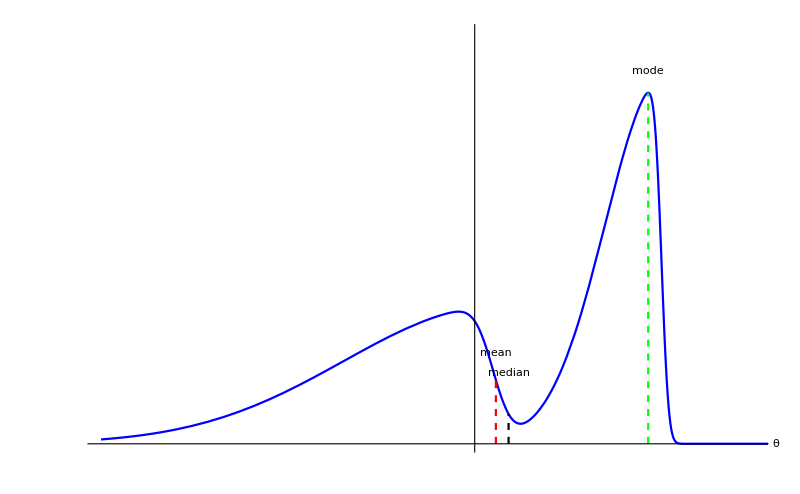

```mathematica
findMode[aDist_,aLower_,aUpper_]:=Module[{lAnswers=Quiet@NSolve[{D[PDF[aDist,x],x]==0,aLower<x<aUpper},x,Reals][[All,1,2]],lpdfValue },lpdfValue = PDF[aDist,#]&/@lAnswers; Extract[lAnswers,Position[lpdfValue,Max[lpdfValue]][[1]]]]
aDist = MixtureDistribution[{0.5,0.5},{SkewNormalDistribution[10,3,-10],SkewNormalDistribution[1,8,-10]}];
gFinal=Module[{aMode = findMode[aDist,0,10]},Show[Plot[PDF[aDist,x],{x,-20,20},Axes->{True,False},PlotRange->{{-20,15},{0,0.15}},Ticks->{False,False},Epilog->{{Dashed,Red,Thickness[0.002],Line[{{N@Mean@aDist,0},{N@Mean@aDist,PDF[aDist,N@Mean@aDist]}}]},{Dashed,Thickness[0.002],Black,Line[{{N@Median@aDist,0},{N@Median@aDist,PDF[aDist,N@Median@aDist]}}]},{Dashed,Thickness[0.002],Green,Line[{{aMode,0},{aMode,PDF[aDist,aMode]}}]},Rotate[Text[Style["mean",Medium],{Mean@aDist,PDF[aDist,Mean@aDist]+0.01}],Pi/2],Rotate[Text[Style["median",Medium],{Median@aDist,PDF[aDist,Median@aDist]+0.015}],Pi/2],Rotate[Text[Style["mode",Medium],{aMode,PDF[aDist,aMode]+0.008}],Pi/2]},PlotStyle->Blue,AxesLabel->{"θ"},BaseStyle->Medium],ImageSize->800]]
```

```mathematica
Export["Posterior_meanMedianMAP.pdf",gFinal]
```

Posterior_meanMedianMAP.pdf